# PCA

## Set Parameters

```mathematica
nn=201;
ll=IntegerPart[nn/10];
prec=32;
nData=50;
```

### Matrix Α

```mathematica
Clear[a0,a1,a2]
Α=SparseArray[{Band[{1,1}]-> a0,Band[{1,2}]-> a1,Band[{2,1}]-> a2},{nn,nn}];
γ=1//N[#,prec]&;
λ=4/7//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
```

### Frequencies

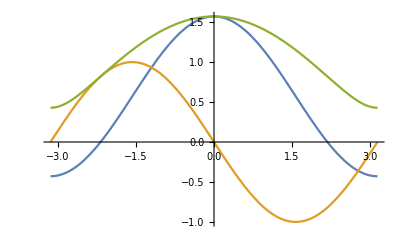

```mathematica
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
Plot[{α[x],β[x],ω[x]},{x,-π,π}]
```

### Matrix B

```mathematica
b[l_]={{α[(2 π l)/nn],-β[(2 π l)/nn]},{β[(2 π l)/nn],α[(2 π l)/nn]}};
bhat[l_]=1/ω[(2 π l)/nn] {{α[(2 π l)/nn],-β[(2 π l)/nn]},{β[(2 π l)/nn],α[(2 π l)/nn]}};
B=ConstantArray[0,{nn,nn}];
B[[1,1]]=N[α[0],prec];
B[[nn,nn]]=N[α[π],prec];
Table[B[[2 k;;1+2 k,2 k;;1+2 k]]=N[b[k],prec];,{k,1,nn/2-1}];
(*B//MatrixForm;*)
Bhat=ConstantArray[0,{nn,nn}];
Bhat[[1,1]]=N[α[0]/ω[0],prec];
Bhat[[nn,nn]]=N[α[π]/ω[π],prec];
Table[Bhat[[2 k;;1+2 k,2 k;;1+2 k]]=N[bhat[k],prec];,{k,1,nn/2-1}];
```

## Diagonalization

### RDFT

```mathematica
(*Ω=E^(I (2 π)/nn);
v1=Table[Ω^k,{k,0,nn-1}];
(U=Table[v1^l/Sqrt[nn],{l,0,nn-1}])//MatrixForm;
Ort=Flatten[Table[Sqrt[2] {Im[U][[i]],Re[U][[i]]},{i,2,nn/2}],1];
(Ortt=Insert[Ort,Re[U][[1]],1])//MatrixForm;
(Orttt=Insert[Ortt,Re[U][[nn/2+1]],nn])//MatrixForm;*)
OFourier=ConstantArray[0,{nn,nn}];
Table[If[l>1,OFourier[[l+1,k+1]]=N[Sqrt[2/nn] Cos[(π l)/nn k],prec],OFourier[[1,k+1]]=N[Sqrt[1/nn] Cos[(π l)/nn k],prec]],{l,0,nn-1,2},{k,0,nn-1}];
Table[If[l<nn-2,OFourier[[l+2,k+1]]=N[Sqrt[2/nn] Sin[(2 π (l/2+1))/nn k],prec],OFourier[[nn,k+1]]=N[Sqrt[1/nn] Cos[π k],prec]],{l,0,nn-1,2},{k,0,nn-1}];
(*OFourier//MatrixForm;
OFourier.Transpose[OFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;*)
(*(QFourier=ArrayFlatten[{{OFourier,0},{0,OFourier}}])//MatrixForm;
(A=ArrayFlatten[{{0,Α},{-Transpose[Α],0}}])//MatrixForm;*)
(*OFourier.Α.Transpose[OFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;
OFourier.Transpose[Α].Transpose[OFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;
B//MatrixForm;
QFourier.A.Transpose[QFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;*)
```

### Full Transformation

```mathematica
(*(Q2=ArrayFlatten[{{Transpose[B1hat],0},{0,IdentityMatrix[nn]}}])//MatrixForm;*)(*bigO=Q2.QFourier;
bigO.Transpose[bigO]//MatrixForm//Chop[#,10^(-prec+1)]&;*)(*(W=bigO.A.Transpose[bigO])//MatrixForm//Chop[#,10^(-prec+1)]&;*)(o1=(Bhat//Transpose).OFourier)//MatrixForm;
(o2=(OFourier//Transpose))//MatrixForm;
o1rect=Take[Take[#,ll]&/@o1,nn];
o2rect=Take[Take[#,nn]&/@o2,ll];
(*o1.Α.o2//MatrixForm//Chop[#,10^(-prec+2)]&;*)
```

## Random Excited States

```mathematica
Now
μ=2//N[#,prec]&;
p[l_]=1/(Exp[β1 (ω[(2 π)/nn l]-μ)]+1);
DataCentered=Table[
β1=RandomReal[{1/5,1/4}]//N[#,prec]&;
MDiag=Table[If[RandomReal[]>p[i],-(1/2),1/2],{i,1,nn}];
(*
Total[MDiag];
*)
MEspRed=(Take[MDiag,ll]*o2rect).o1rect;
Flatten[MEspRed]-Mean[Flatten[MEspRed]]
,{ii,nData}];
Now
```

Wed 18 Apr 2018 14:14:42

Wed 18 Apr 2018 14:14:46

```mathematica
Cov=Sum[TensorProduct[DataCentered⟦i⟧,DataCentered⟦i⟧],{i,nData}]//Timing;
Cov⟦1⟧
```

9.196

```mathematica
EigenCov=Eigensystem[Cov⟦2⟧]//Timing;
EigenCov⟦1⟧
```

299.56

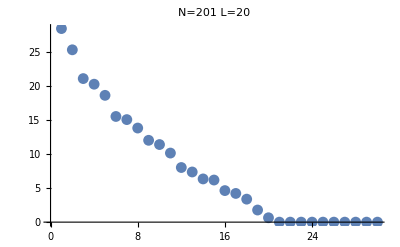

```mathematica
ListPlot[EigenCov⟦2,1⟧//Take[#,30]&,PlotRange->All,PlotLabel->"N=201  L=20"]
```

```mathematica
M1=Partition[EigenCov⟦2,2,1⟧,ll];
M2=Partition[EigenCov⟦2,2,2⟧,ll];
MatrixRank[M1]
Length[M1]
MatrixRank[M2]
Length[M2]
```

20

20

20

«1 more identical outputs»

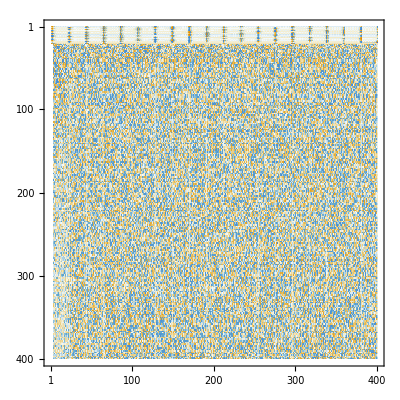

```mathematica
MatrixPlot[EigenCov⟦2,2⟧]
```

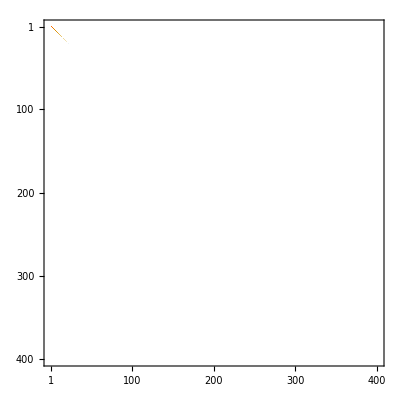

```mathematica
EigenCov⟦2,1⟧//DiagonalMatrix//MatrixPlot
```

```mathematica
EigenCov⟦2,1⟧⟦100⟧//Log
```

-129.09936059849069177411187-1.83000194898433582240553 ⅈ

```mathematica
Table[Subscript[a,i,j],{i,3},{j,3}]//MatrixForm
%//Flatten
%//Partition[#,2]&//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

{a_(1,1),a_(1,2),a_(1,3),a_(2,1),a_(2,2),a_(2,3),a_(3,1),a_(3,2),a_(3,3)}

(a_(1,1) | a_(1,2)
a_(1,3) | a_(2,1)
a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2))

```mathematica
√200//N
```

14.1421

```mathematica
vv=Table[Subscript[v, i],{i,0,4}];
uu=Table[Subscript[u, Mod[i+2,5]],{i,0,4}];
(V=Table[RotateRight[vv,j-1],{j,5}])//MatrixForm;
(U=Table[RotateLeft[uu,j-1],{j,5}])//MatrixForm;
V+U//MatrixForm
Z=Table[RotateRight[vv,j-1],{j,5}]+Table[RotateLeft[uu,j-1],{j,5}]//MatrixForm
```

(u_2+v_0 | u_3+v_1 | u_4+v_2 | u_0+v_3 | u_1+v_4
u_3+v_4 | u_4+v_0 | u_0+v_1 | u_1+v_2 | u_2+v_3
u_4+v_3 | u_0+v_4 | u_1+v_0 | u_2+v_1 | u_3+v_2
u_0+v_2 | u_1+v_3 | u_2+v_4 | u_3+v_0 | u_4+v_1
u_1+v_1 | u_2+v_2 | u_3+v_3 | u_4+v_4 | u_0+v_0)

(u_2+v_0 | u_3+v_1 | u_4+v_2 | u_0+v_3 | u_1+v_4
u_3+v_4 | u_4+v_0 | u_0+v_1 | u_1+v_2 | u_2+v_3
u_4+v_3 | u_0+v_4 | u_1+v_0 | u_2+v_1 | u_3+v_2
u_0+v_2 | u_1+v_3 | u_2+v_4 | u_3+v_0 | u_4+v_1
u_1+v_1 | u_2+v_2 | u_3+v_3 | u_4+v_4 | u_0+v_0)

```mathematica
Join[vv,uu]
```

{v_0,v_1,v_2,v_3,v_4,u_2,u_3,u_4,u_0,u_1}